## Prelab 5 Francesco Vassalli

### Q1

G_0:

-9.9956

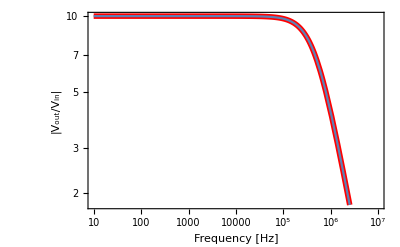

```mathematica
Subscript[A, 0]=25*10^3;
f0=fT/Subscript[A, 0];
R=10^4;
Rf=10^5;
B=R/(R+Rf);
G0=-Subscript[A, 0](1-B)/(1+Subscript[A, 0]*B);
"G_0:"
N[G0]
A[f_]:=Subscript[A, 0]/(1+ⅉ*f/f0);
openLoop[f_]:=Abs[-A[f](1-B)/(1+A[f]*B)];
fT=5*10^6;
fB=fT*(1-B)/-G0;
closedLoop[f_]:=Abs[G0/(1+ⅉ*f/fB)];
openplot=LogLogPlot[openLoop[f],{f,10,10^7},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency [Hz]", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},GridLines->All];
closedplot=LogLogPlot[closedLoop[f],{f,10,10^7}];
Show[openplot,closedplot]
```

### Q2

Response in appendix.

### Q3

Response in appendix.

### Q4

This lab looks cool.  There isn’t much direction for the integrator which will be hard.  I’m curious what an ADC looks like.